FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

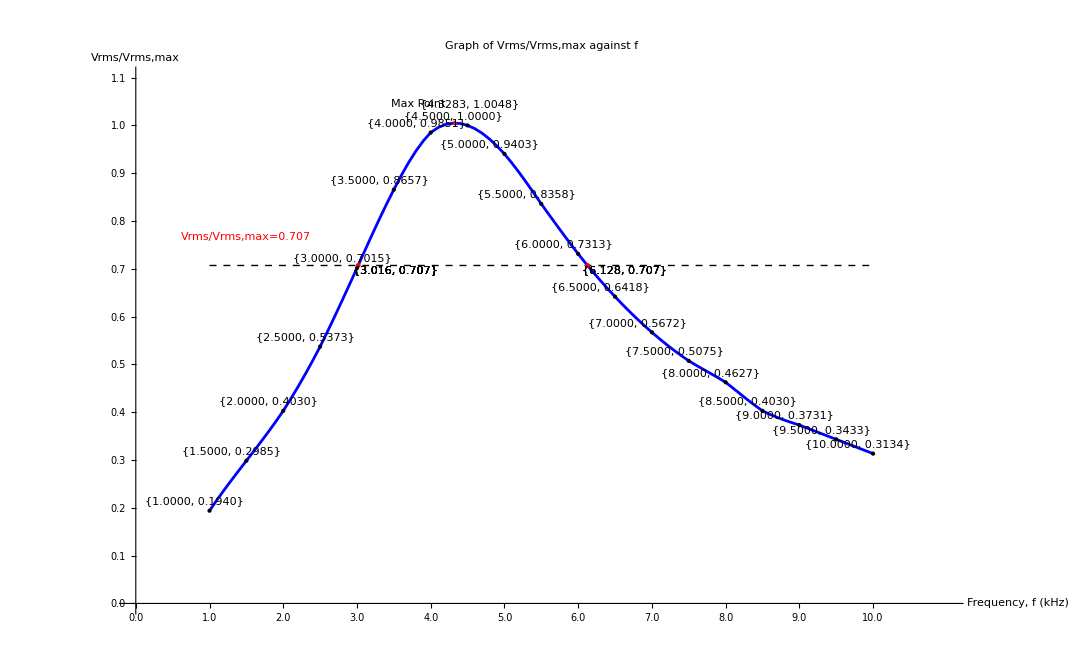

```mathematica
data={{1.0,0.1940},{1.5,0.2985},{2.0,0.4030},{2.5,0.5373},{3.0,0.7015},{3.5,0.8657},{4.0,0.9851},{4.5,1.0000},{5.0,0.9403},{5.5,0.8358},{6.0,0.7313},{6.5,0.6418},{7.0,0.5672},{7.5,0.5075},{8.0,0.4627},{8.5,0.4030},{9.0,0.3731},{9.5,0.3433},{10.0,0.3134}};

smoothCurve=Interpolation[data];

(*Find the maximum point on the smooth curve*)
maxPoint={x,smoothCurve[x]}/. FindMaximum[smoothCurve[x],{x,4.50}][[2]];

intersectionPoints={x,0.707}/. Table[FindRoot[smoothCurve[x]==0.707,{x,xi}],{xi,1,10,1}];

ListLinePlot[{Table[{x,smoothCurve[x]},{x,1,10,0.1}]},PlotStyle->Blue,AxesLabel->{"Frequency, f (kHz)","Vrms/Vrms,max"},PlotLabel->"Graph of Vrms/Vrms,max against f",Epilog->{Dashed,Line[{{1,0.707},{10,0.707}}],Red,PointSize[Medium],Point[intersectionPoints],Text[Style[ToString@NumberForm[#,{4,3}],Black],#+{0.5,-0.01}]&/@intersectionPoints,Text["Vrms/Vrms,max=0.707",{1.5,0.707+0.06}],Text[Style[ToString@NumberForm[#,{4,4}],Black],#+{-0.2,0.02}]&/@data,Text[Style["Max Point",Black],maxPoint+{-0.5,0.04}],Red,PointSize[Medium],Point[{maxPoint}],Text[Style[ToString@NumberForm[maxPoint,{5,4}],Black],maxPoint+{0.2,0.04}],Black,PointSize[Medium],Point[data]},PlotRange->{{0,11.0},{0,1.1}},Ticks->{{#,NumberForm[#,{3,1}]}&/@Range[0,10.5,0.5],{#,NumberForm[#,{3,1}]}&/@Range[0,1.1,0.1]}]
```